```mathematica
(*data =Import[StringJoin[$HomeDirectory,"/Dropbox/PostDoc/2020_Sevilleta2/data/scaled_eigenvecs_sigma1_r1000b_4wks_new.csv"]];*)
```

```mathematica
(*tid =Flatten[Import[StringJoin[$HomeDirectory,"/Dropbox/PostDoc/2020_Sevilleta2/data/tid_sigma1_r1000b_4wks_new.csv"]],1];*)
```

```mathematica
data =Import[StringJoin[$HomeDirectory,"/Dropbox/PostDoc/2020_Sevilleta2/data/scaled_eigenvecs_sigma1_r1000b_4wks_resourceset.csv"]];
tid =Flatten[Import[StringJoin[$HomeDirectory,"/Dropbox/PostDoc/2020_Sevilleta2/data/tid_sigma1_r1000b_4wks_resourceset.csv"]],1];
```

```mathematica
interpolatedata={{#[[1]],#[[2]]},#[[3]]}&/@data;
```

```mathematica
scaledinterpolatedata = interpolatedata;
scaledinterpolatedata[[All,2]] = ((interpolatedata[[All,2]])/Max[interpolatedata[[All,2]]]);
```

```mathematica
scaleddata = data;
scaledfitness = Log[(((interpolatedata[[All,2]])/Max[interpolatedata[[All,2]]]))*100];
scaleddata[[All,3]] = scaledfitness;
```

```mathematica
hexToRGB=RGBColor@@(IntegerDigits[#~StringDrop~1~FromDigits~16,256,3]/255.)&
```

RGBColor@@IntegerDigits[FromDigits[StringDrop[#1,1],16],256,3]/255.&

```mathematica
scaleddata//MatrixForm
```

(2.74709 | 0.957996 | 4.59462
2.74598 | 0.95768 | 4.60222
2.74503 | 0.957415 | 4.60494
2.71238 | 0.94861 | 4.60516
2.70802 | 0.947451 | 4.60517
2.70765 | 0.947355 | 4.60517
8.17973 | 2.49667 | 3.06476
-0.0721349 | -4.49098 | 2.11457
-3.10059 | -1.68794 | 1.30179
-3.85299 | -0.450867 | 0.848888
-3.60705 | -0.56409 | 0.49274
8.06724 | 2.21069 | 3.72294
4.28828 | -0.184518 | 3.54834
3.55297 | 0.122429 | 3.59037
2.64787 | 0.401016 | 3.77987
2.4454 | 0.500363 | 3.92375
2.75574 | 0.960513 | 4.48078
3.21967 | 1.11228 | 4.1789
7.82194 | 2.20937 | 2.55818
3.58638 | -3.51843 | 0.50757
-2.14204 | -0.0387875 | -0.48914
7.89542 | 2.12493 | 3.18851
1.66256 | -4.71799 | 1.92101
-1.95071 | -2.20982 | 0.41585
-4.57023 | 0.566816 | -0.568812
-3.89147 | 1.01734 | -0.738344
8.24804 | 2.41499 | 2.51141
1.49141 | -5.76275 | 0.702844
-4.56178 | -0.155419 | -0.414937
-5.32818 | 2.48504 | -0.757277
-4.11032 | 1.65271 | -0.798031
8.20014 | 2.51341 | 3.13801
0.718805 | -5.26796 | 2.47866
-0.794014 | -3.77652 | 2.4069
-2.81579 | -1.99404 | 2.53719
-3.01484 | -1.74614 | 2.84369
8.10392 | 2.23397 | 3.82073
6.24984 | 0.395445 | 3.89582
4.32108 | -0.187432 | 4.06141
3.94162 | 0.0565129 | 4.1693
3.86489 | 0.0752329 | 4.24205
2.74633 | 0.957777 | 4.57978
2.74525 | 0.957476 | 4.60066
2.7445 | 0.95727 | 4.60427
2.71221 | 0.948564 | 4.60504
2.71194 | 0.948491 | 4.60516
7.8912 | 2.11763 | 3.45921
4.00101 | -2.03877 | 3.31486
0.456165 | -3.63608 | 3.32207
-0.681856 | -2.52737 | 3.31608
-2.39228 | -1.56396 | 3.33607
8.24543 | 2.40738 | 2.54201
1.69119 | -5.24643 | 0.985917
-0.638429 | -3.57666 | 0.135469
-2.96481 | -1.39514 | -0.343284
-3.12303 | -1.19827 | -0.520717
8.21459 | 2.50673 | 2.69831
1.16182 | -5.7825 | 1.51301
-5.05331 | 0.925719 | 1.0448
-5.5669 | 2.9208 | 1.09543
-4.58669 | 3.1086 | 1.36882
8.14468 | 2.49926 | 2.94205
0.481013 | -5.09854 | 1.73076
-2.89342 | -1.91329 | 0.859765
-3.86207 | -0.462116 | 0.301677
-3.61733 | -0.554597 | -0.0449875
8.20729 | 2.51358 | 2.43499
0.836866 | -5.50078 | 0.804083
-3.90679 | -0.662034 | -0.141684
-5.30408 | 2.471 | -0.514699
-3.76841 | 1.2999 | -0.675637
8.26699 | 2.5144 | 2.25651
1.1083 | -5.76317 | 0.411214
-4.34351 | -0.2751 | -0.558992
-5.57531 | 2.84553 | -0.731071
-3.11262 | 2.05972 | -0.820697
8.08705 | 2.23583 | 3.50451
4.30991 | -0.198515 | 2.88422
3.58491 | 0.111212 | 2.57988
2.48898 | 0.453377 | 2.25418
2.43349 | 0.503821 | 1.86113
8.27448 | 2.46001 | 2.44784
2.65761 | -3.08514 | 0.809815
-4.70032 | 0.121752 | -0.100549
-4.63968 | 2.37742 | -0.552284
-1.98605 | 2.26109 | -0.701072
8.26726 | 2.5076 | 2.35611
1.47531 | -5.66578 | 0.507724
-4.61136 | -0.0117905 | -0.519854
-5.43392 | 2.8462 | -0.721206
-3.99569 | 3.21592 | -0.798031
8.21521 | 2.41626 | 2.93346
1.87504 | -4.96085 | 1.32476
-3.55167 | -0.883604 | 0.064133
-4.85342 | 0.959456 | -0.728413
-4.45096 | 1.07209 | -0.768135
8.27552 | 2.48169 | 2.47583
1.64795 | -5.56746 | 0.709972
-4.50197 | -0.20755 | -0.420025
-5.33959 | 1.91162 | -0.746917
-4.77122 | 1.59071 | -0.789346
8.2824 | 2.48111 | 2.36723
1.4492 | -5.80352 | 0.438344
-4.34255 | -0.35587 | -0.762492
-5.36393 | 2.39956 | -0.930862
-4.13915 | 1.65463 | -0.902862
8.25244 | 2.5048 | 2.68627
1.32649 | -5.74151 | 1.68682
-4.78503 | 0.259712 | 1.54354
-5.79968 | 2.61441 | 1.82227
-5.20743 | 3.09901 | 2.17666
8.1697 | 2.50641 | 2.9511
0.732314 | -5.33936 | 2.15494
-1.10405 | -3.47597 | 1.90395
-2.60943 | -2.19224 | 1.93128
-3.31444 | -1.28695 | 2.16957
8.1709 | 2.50554 | 2.42848
1.15067 | -5.78662 | 0.926494
-3.98 | -0.59656 | 0.532654
-5.55356 | 2.58746 | 0.674525
-3.99343 | 2.09303 | 0.808315
8.29935 | 2.35737 | 2.2833
1.18301 | -5.84949 | 0.451323
-4.40313 | -0.253699 | -0.331243
-5.64698 | 2.66109 | -0.552457
-3.06231 | 2.05646 | -0.494535
8.20271 | 2.39074 | 3.55576
6.10017 | -0.223157 | 3.53301
4.42381 | -0.233529 | 3.8037
4.02552 | 0.02998 | 4.02216
3.86786 | 0.0739808 | 4.12523
8.25612 | 2.50533 | 2.4567
1.91932 | -5.00242 | 0.99429
-4.52674 | -0.124492 | 0.489658
-5.49843 | 2.22738 | 0.482802
-4.89634 | 2.87436 | 0.636966
8.23862 | 2.5176 | 2.32939
1.40368 | -5.77914 | 0.523103
-4.57516 | -0.0665709 | -0.328472
-5.58348 | 2.72592 | -0.565232
-4.40702 | 3.34593 | -0.460956
7.88241 | 2.11407 | 3.23998
4.00254 | -2.04102 | 2.98324
-0.0248718 | -3.10744 | 2.86031
-0.837402 | -2.35479 | 2.84649
-2.38355 | -1.5634 | 2.79716
8.29482 | 2.49827 | 2.48177
1.7818 | -5.22278 | 0.919821
-0.496763 | -3.8709 | -0.0883578
-3.06674 | -1.32708 | -0.521592
-3.50342 | -0.936684 | -0.761635
8.28252 | 2.47341 | 2.38175
1.47704 | -5.54483 | 0.605239
-3.08268 | -1.20124 | -0.363876
-4.86496 | 0.956947 | -0.725109
-3.51419 | -1.08551 | -0.877111
8.29419 | 2.4947 | 2.67198
1.18998 | -5.79931 | 1.33489
-4.84377 | 0.378841 | 0.631099
-5.61062 | 2.89621 | 0.584781
-4.65736 | 3.22251 | 0.759163
8.26236 | 2.50555 | 2.30056
1.39412 | -5.85813 | 0.389643
-4.54811 | -0.0990049 | -0.525582
-5.62469 | 2.81266 | -0.631284
-2.80528 | 1.65534 | -0.575229
8.18098 | 2.50655 | 2.24257
1.39596 | -5.84327 | 0.194708
-4.37933 | -0.141739 | -0.695731
-5.55346 | 2.78264 | -0.75553
-2.47729 | 1.11942 | -0.825825
8.23117 | 2.51869 | 2.43381
0.844937 | -5.5157 | 0.601153
-3.98668 | -0.592997 | -0.210676
-5.47624 | 2.57961 | -0.629578
-3.72011 | 1.44909 | -0.778232
8.24008 | 2.51795 | 2.2935
1.23247 | -5.82164 | 0.328482
-4.46147 | -0.188681 | -0.619974
-5.58834 | 2.83173 | -0.802785
-2.95272 | 1.96422 | -0.783381
8.26294 | 2.51644 | 2.22209
1.26439 | -5.83417 | 0.19504
-4.4307 | -0.208134 | -0.799322
-5.60976 | 2.78701 | -0.87254
-2.64688 | 1.55441 | -0.988574
8.27994 | 2.47041 | 2.43497
1.91812 | -5.00049 | 0.657927
-4.64518 | 0.0316788 | -0.20892
-5.22209 | 2.7051 | -0.56292
-2.66509 | 2.48503 | -0.712732
8.27599 | 2.51402 | 2.2633
1.51271 | -5.61937 | 0.478455
-4.59239 | -0.0323373 | -0.465823
-5.48849 | 2.844 | -0.765226
-3.97108 | 3.38733 | -0.76567
8.21478 | 2.51334 | 2.2269
1.3694 | -5.82476 | 0.220093
-4.53247 | -0.0836116 | -0.786436
-5.52203 | 2.79268 | -0.920394
-3.0479 | 2.07065 | -0.913445
8.25199 | 2.44132 | 2.37318
1.57416 | -5.69303 | 0.290182
-4.47122 | -0.249251 | -0.709829
-5.38569 | 2.45841 | -0.929823
-4.6714 | 1.5148 | -0.894029
8.20849 | 2.51013 | 2.65396
1.27684 | -5.8156 | 1.28868
-4.62686 | 0.0106781 | 0.938602
-5.82662 | 2.56742 | 1.20844
-4.9268 | 3.11471 | 1.53918
8.26471 | 2.45355 | 2.31393
1.27519 | -5.82776 | 0.46492
-4.45178 | -0.186014 | -0.431203
-5.60087 | 2.73051 | -0.55137
-2.61806 | 1.32656 | -0.472053
8.25535 | 2.51806 | 2.19725
1.30921 | -5.81675 | 0.237192
-4.4406 | -0.16477 | -0.651833
-5.50303 | 2.76042 | -0.770675
-2.23017 | 0.929387 | -0.808342
8.21859 | 2.51518 | 2.39375
1.05869 | -5.71613 | 0.852347
-4.21636 | -0.419634 | 0.202686
-5.56265 | 2.66545 | 0.208404
-3.83049 | 2.18347 | 0.33423
8.27715 | 2.49755 | 2.26206
1.4219 | -5.77387 | 0.359929
-4.31199 | -0.361865 | -0.499739
-5.66205 | 2.66025 | -0.664821
-2.78414 | 1.62719 | -0.61207
8.29283 | 2.5064 | 2.2436
1.32931 | -5.85163 | 0.173238
-4.40966 | -0.209303 | -0.708088
-5.58904 | 2.65339 | -0.809353
-2.71854 | 1.46699 | -0.817924
8.2698 | 2.50987 | 2.42742
1.70873 | -5.52041 | 0.818452
-4.43165 | -0.267506 | 0.143275
-5.43927 | 2.5198 | 0.161048
-4.83354 | 2.97797 | 0.19094
8.29825 | 2.48159 | 2.31385
1.41276 | -5.80684 | 0.496245
-4.55653 | -0.0805633 | -0.416204
-5.59202 | 2.71564 | -0.618362
-3.82848 | 3.07029 | -0.640209
8.19976 | 2.5099 | 2.26376
1.31856 | -5.76959 | 0.156846
-4.47239 | -0.205096 | -0.722332
-5.55843 | 2.70885 | -0.7956
-2.90869 | 1.69119 | -0.815389
8.27661 | 2.51675 | 2.3043
1.36034 | -5.68571 | 0.452942
-3.69213 | -0.835426 | -0.549503
-4.9061 | 1.03237 | -0.797773
-3.39509 | -1.25074 | -0.904839
8.28724 | 2.49468 | 2.2317
1.30277 | -5.78175 | 0.330895
-4.47489 | -0.16604 | -0.556831
-5.57557 | 2.78214 | -0.789794
-2.63471 | 1.36152 | -0.732124
8.27614 | 2.51195 | 2.23117
1.22643 | -5.86122 | 0.205191
-4.43881 | -0.156365 | -0.814074
-5.52285 | 2.74651 | -0.811927
-2.27242 | 0.954522 | -0.809474
8.23062 | 2.51609 | 2.17176
1.23694 | -5.84107 | -0.0379968
-4.41834 | -0.20501 | -0.85415
-5.51386 | 2.72909 | -0.971998
-2.08685 | 0.883285 | -0.926371
8.27455 | 2.51522 | 2.21692
1.27327 | -5.82506 | 0.224818
-4.4976 | -0.144248 | -0.850736
-5.59121 | 2.78122 | -0.980364
-2.71395 | 1.71868 | -0.93712
8.28907 | 2.50958 | 2.22601
1.32449 | -5.87025 | 0.214647
-4.49073 | -0.161413 | -0.67432
-5.54119 | 2.79214 | -0.915913
-3.01622 | 2.04509 | -0.878933
8.24001 | 2.51321 | 2.19224
1.12346 | -5.81864 | 0.216754
-4.42912 | -0.22114 | -0.526267
-5.57297 | 2.71737 | -0.637831
-2.38379 | 1.03373 | -0.657891
8.26836 | 2.51888 | 2.18296
1.3001 | -5.8147 | 0.215331
-4.4136 | -0.217772 | -0.657059
-5.52646 | 2.76864 | -0.813962
-2.07627 | 0.816495 | -0.825966
8.28766 | 2.51028 | 2.16326
1.41617 | -5.84285 | 0.090378
-4.41187 | -0.142294 | -0.863828
-5.54538 | 2.68456 | -0.94227
-1.00885 | 0.707647 | -0.963442
8.27314 | 2.51257 | 2.20841
1.31357 | -5.82561 | 0.207018
-4.43018 | -0.232716 | -0.855244
-5.54365 | 2.71795 | -0.891035
-2.58846 | 1.34252 | -0.950479
8.2927 | 2.48458 | 2.21952
1.29679 | -5.85975 | 0.25206
-4.41688 | -0.153336 | -0.772572
-5.54922 | 2.73934 | -0.910931
-2.65478 | 1.37974 | -0.851193
8.21426 | 2.51319 | 2.14222
1.2406 | -5.83538 | 0.0059609
-4.421 | -0.158589 | -0.909675
-5.45123 | 2.74102 | -0.987527
-0.922755 | 0.714886 | -0.934544
8.26701 | 2.51537 | 2.15109
1.36413 | -5.80098 | -0.0214077
-4.4279 | -0.152834 | -0.863059
-5.45649 | 2.7398 | -0.955848
-0.469654 | 0.921838 | -0.930517)

```mathematica
rescaledfitness = (scaledfitness-Min[scaledfitness])/(Max[scaledfitness]-Min[scaledfitness])
```

{0.998114,0.999473,0.999958,0.999998,1.,1.,0.724619,0.554753,0.409451,0.328485,0.264816,0.842282,0.811068,0.818582,0.852461,0.878182,0.977763,0.923796,0.634057,0.267467,0.0892844,0.746743,0.520149,0.25107,0.0750414,0.0447341,0.625695,0.302377,0.10255,0.0413493,0.0340636,0.737714,0.619842,0.607012,0.630304,0.685098,0.859765,0.87319,0.902791,0.92208,0.935084,0.995462,0.999194,0.999838,0.999976,0.999998,0.795136,0.769329,0.77062,0.769547,0.773121,0.631167,0.352982,0.200946,0.115359,0.0836394,0.659109,0.447211,0.363509,0.372559,0.421434,0.702683,0.486138,0.33043,0.23066,0.168686,0.612035,0.320475,0.151399,0.0847152,0.0559441,0.580127,0.250242,0.0767969,0.0460342,0.0300116,0.803234,0.692344,0.637937,0.57971,0.509444,0.614332,0.3215,0.158753,0.0779962,0.0513971,0.597932,0.267495,0.0837937,0.0477977,0.0340637,0.701147,0.413557,0.188194,0.0465094,0.0394081,0.619335,0.303651,0.10164,0.0432014,0.0356163,0.59992,0.255092,0.040417,0.0103173,0.0153229,0.656956,0.478283,0.45267,0.502498,0.565852,0.704299,0.561969,0.5171,0.521986,0.564584,0.610871,0.342359,0.271952,0.297314,0.321232,0.584916,0.257412,0.117512,0.0779653,0.08832,0.812395,0.808328,0.85672,0.895774,0.9142,0.615916,0.354479,0.264265,0.26304,0.2906,0.593156,0.270244,0.118007,0.0756815,0.0943229,0.755943,0.710046,0.68807,0.685599,0.67678,0.620397,0.341166,0.160933,0.083483,0.0405703,0.602517,0.284928,0.111678,0.0471,0.0199265,0.654401,0.415368,0.289551,0.281271,0.312445,0.588003,0.246386,0.0827697,0.0638733,0.0738942,0.577636,0.211537,0.052352,0.0416616,0.0290949,0.611823,0.284197,0.139066,0.0641782,0.0376031,0.586741,0.235452,0.0658951,0.0332138,0.0366826,0.573974,0.211596,0.0338329,0.0207436,0.,0.612031,0.294347,0.13938,0.0760947,0.0493127,0.581342,0.262263,0.0934529,0.0399282,0.0398488,0.574834,0.216075,0.0361365,0.0121886,0.013431,0.600985,0.228605,0.0498316,0.0105031,0.0169021,0.65118,0.407107,0.344524,0.392764,0.45189,0.590393,0.259843,0.099642,0.0781596,0.0923392,0.569533,0.219132,0.0601996,0.0389542,0.0322204,0.604663,0.329104,0.212963,0.213985,0.236479,0.58112,0.241073,0.0873896,0.0578777,0.0673081,0.577819,0.207699,0.0501429,0.0320396,0.0305075,0.610681,0.323044,0.202342,0.205519,0.210863,0.590379,0.265443,0.102323,0.0661833,0.0622777,0.581423,0.204768,0.0475964,0.0344983,0.0309606,0.58867,0.257701,0.0784934,0.0341097,0.0149694,0.575692,0.235883,0.0771832,0.0355362,0.0458459,0.575597,0.213411,0.0311957,0.0315794,0.0320181,0.564977,0.169936,0.0240312,0.00296332,0.0111202,0.573049,0.216919,0.0246415,0.00146784,0.00919853,0.574675,0.215101,0.0561797,0.0129897,0.0196007,0.568637,0.215478,0.0826473,0.0627028,0.0591167,0.566978,0.215224,0.0592653,0.0312156,0.0290696,0.563456,0.192886,0.0223011,0.00827787,0.00449297,0.571528,0.213737,0.0238356,0.0174373,0.00681036,0.573514,0.22179,0.038615,0.0138803,0.0245598,0.559696,0.177794,0.0141049,0.000187273,0.00965906,0.561281,0.172901,0.0224386,0.00585051,0.0103791}

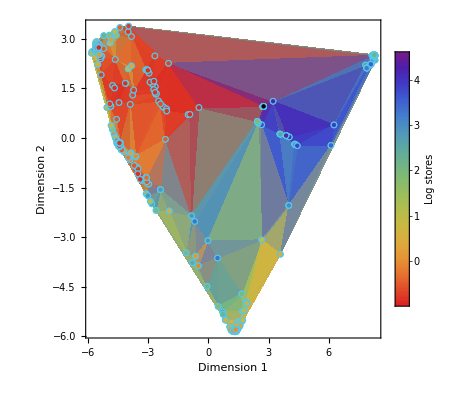

```mathematica
(*nr=6;*)
(*corners = {{-1.6,-2,0.65},{-1.6,1.8,0.6},{3,-2,1.15},{3,1.8,0.38}};*)
colorkey = ColorData[{"Rainbow","Reverse"}][#]&/@(rescaledfitness);
PointData =Table[{scaledinterpolatedata[[i,1]]},{i,1,Length[scaledinterpolatedata[[All,1]]]}];
InterpolatePlot = Show[{
ListDensityPlot[Join[scaleddata],InterpolationOrder->5,Mesh->None,ColorFunction->ColorData[{"Rainbow","Reverse"}],PlotLegends->BarLegend[Automatic,LegendLabel->"Log stores"],PlotRange->All,FrameLabel->{"Dimension 1","Dimension 2"},LabelStyle->Directive[FontSize->16]],
Table[ListPlot[PointData[[i]],PlotMarkers->{Graphics[{EdgeForm[{hexToRGB["#55C9E9"],Thick}],FaceForm[colorkey[[i]]],Disk[]}],0.04}],{i,1,Length[colorkey]}],
ListPlot[PointData[[1]],PlotMarkers->{Graphics[{EdgeForm[{hexToRGB["#55C9E9"],Thick}],FaceForm[Black],Disk[]}],0.04}]
}]
```

```mathematica
Export[StringJoin[$HomeDirectory,"/Dropbox/PostDoc/2020_Sevilleta2/figures2/fig_fitnessmanifold_interp_sigma1_r1000_smooth_resourceset.pdf"],InterpolatePlot]
```

/home/jdyeakel/Dropbox/PostDoc/2020_Sevilleta2/figures2/fig_fitnessmanifold_interp_sigma1_r1000_smooth_resourceset.pdf

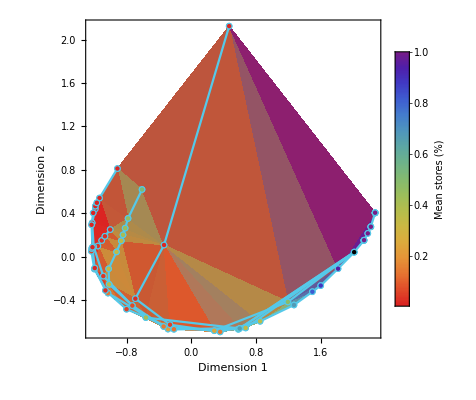

```mathematica
nr=6;
corners = {{-1.6,-2,0.65},{-1.6,1.8,0.6},{3,-2,1.15},{3,1.8,0.38}};
colorkey = ColorData[{"Rainbow","Reverse"}][#]&/@(scaledinterpolatedata[[All,2]]);
PointData =Table[{scaledinterpolatedata[[i,1]]},{i,1,Length[scaledinterpolatedata[[All,1]]]}];
InterpolatePlot = Show[{
ListDensityPlot[Join[scaleddata],InterpolationOrder->1,Mesh->None,ColorFunction->ColorData[{"Rainbow","Reverse"}],PlotLegends->BarLegend[Automatic,LegendLabel->"Mean stores (%)"],PlotRange->All,FrameLabel->{"Dimension 1","Dimension 2"},LabelStyle->Directive[FontSize->16]],
Table[
findtids = Flatten[Position[tid,i],1];
xspline = Join[{scaleddata[[1,1]]},scaleddata[[findtids,1]]];
yspline =  Join[{scaleddata[[1,2]]},scaleddata[[findtids,2]]];
ListPlot[Transpose[{xspline,yspline}],Joined->True,PlotStyle->{hexToRGB["#55C9E9"],Thick},PlotRange->All],
{i,1,nr}],
Table[ListPlot[PointData[[i]],PlotMarkers->{Graphics[{EdgeForm[{hexToRGB["#55C9E9"],Thick}],FaceForm[colorkey[[i]]],Disk[]}],0.05}],{i,1,Length[colorkey]}],
ListPlot[PointData[[1]],PlotMarkers->{Graphics[{EdgeForm[{hexToRGB["#55C9E9"],Thick}],FaceForm[Black],Disk[]}],0.05}]
}]
```

```mathematica
Export[StringJoin[$HomeDirectory,"/Dropbox/PostDoc/2020_Sevilleta2/figures2/fig_fitnessmanifold_interp_sigma1_r1000_smooth_new.pdf"],InterpolatePlot]
```

/home/jdyeakel/Dropbox/PostDoc/2020_Sevilleta2/figures2/fig_fitnessmanifold_interp_sigma1_r1000_smooth_new.pdf

{2.01493,1.81525,1.60053,1.4972,1.26953,0.849874,0.35505,-0.266302,-0.695205,-0.339956,0.466838}

{0.0405843,-0.111529,-0.267506,-0.32419,-0.446325,-0.596653,-0.69445,-0.628352,-0.388095,0.106591,2.12437}

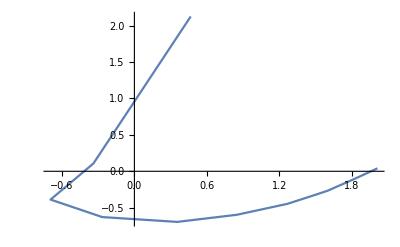

```mathematica
findtids = Flatten[Position[tid,4],1];
xspline = Join[{scaleddata[[1,1]]},scaleddata[[findtids,1]]]
yspline =  Join[{scaleddata[[1,2]]},scaleddata[[findtids,2]]]
ListPlot[Transpose[{xspline,yspline}],Joined->True,PlotRange->All]
```

```mathematica
Transpose[{xspline,yspline}]
```

{{2.01493,0.0405843},{1.81525,-0.111529},{1.60053,-0.267506},{1.4972,-0.32419},{1.26953,-0.446325},{0.849874,-0.596653},{0.35505,-0.69445},{-0.266302,-0.628352},{-0.695205,-0.388095},{-0.339956,0.106591},{0.466838,2.12437}}

```mathematica
tid
```

{0,1,1,1,1,1,1,1,1,1,1,2,2,2,2,2,2,2,2,2,2,3,3,3,3,3,3,3,3,3,3,4,4,4,4,4,4,4,4,4,4,5,5,5,5,5,5,5,5,5,5,6,6,6,6,6,6,6,6,6,6}

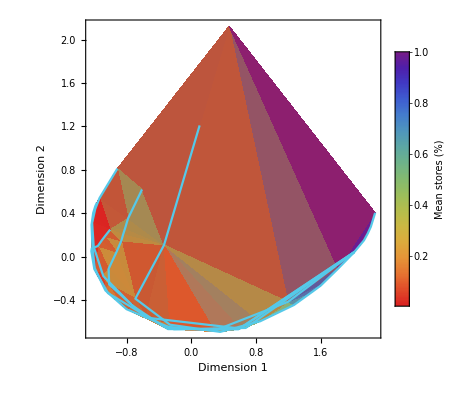

```mathematica
Show[{
ListDensityPlot[Join[scaleddata],InterpolationOrder->1,Mesh->None,ColorFunction->ColorData[{"Rainbow","Reverse"}],PlotLegends->BarLegend[Automatic,LegendLabel->"Mean stores (%)"],PlotRange->All,FrameLabel->{"Dimension 1","Dimension 2"},LabelStyle->Directive[FontSize->16]],
Table[
findtids = Flatten[Position[tid,i],1];
xspline = Join[{scaleddata[[1,1]]},scaleddata[[findtids,1]]];
yspline =  Join[{scaleddata[[1,2]]},scaleddata[[findtids,2]]];
ListPlot[Transpose[{xspline,yspline}],Joined->True,PlotStyle->{hexToRGB["#55C9E9"],Thick}],
{i,1,nr}]}]
```

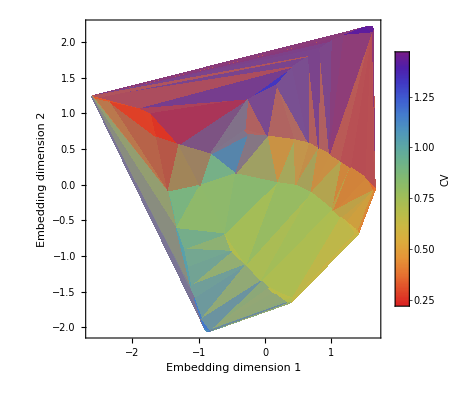

```mathematica
corners = {{-1.6,-2,0.65},{-1.6,1.8,0.6},{3,-2,1.15},{3,1.8,0.38}};
colorkey = ColorData[{"Rainbow","Reverse"}][#]&/@(interpolatedata[[All,2]]/Max[interpolatedata[[All,2]]]);
PointData =Table[{interpolatedata[[i,1]]},{i,1,Length[interpolatedata[[All,1]]]}];
InterpolatePlotNoPts = Show[{
ListDensityPlot[Join[data],InterpolationOrder->1,Mesh->None,ColorFunction->ColorData[{"Rainbow","Reverse"}],PlotLegends->BarLegend[Automatic,LegendLabel->"CV"],PlotRange->All,FrameLabel->{"Embedding dimension 1","Embedding dimension 2"}]
(*Table[ListPlot[PointData[[i]],PlotMarkers->{Graphics[{EdgeForm[{Black,Thick}],FaceForm[colorkey[[i]]],Disk[]}],0.03}],{i,1,Length[colorkey]}],
ListPlot[PointData[[1]],PlotMarkers->{Graphics[{EdgeForm[{Black,Thick}],FaceForm[Black],Disk[]}],0.03}]*)
}]
```

```mathematica
Export[StringJoin[$HomeDirectory,"/Dropbox/PostDoc/2020_Sevilleta2/figures2/fig_fitnessmanifold_interp_sigma1_r1000_smooth_nopts.pdf"],InterpolatePlotNoPts]
```

/home/jdyeakel/Dropbox/PostDoc/2020_Sevilleta2/figures2/fig_fitnessmanifold_interp_sigma1_r1000_smooth_nopts.pdf

```mathematica
ColorData[{"Rainbow","Reverse"}][#]&/@interpolatedata[[All,2]]
```

{RGBColor[0.8798122853355085, 0.6325456095186578, 0.22786141579148975],RGBColor[0.8279102931138764, 0.6967829659073866, 0.24909065077783432],RGBColor[0.7791005637861691, 0.7248570574719424, 0.26744564094430684],RGBColor[0.7697826999485297, 0.7270881773972268, 0.27143652769350435],RGBColor[0.7745779817866189, 0.725939969069359, 0.2693826849802215],RGBColor[0.8074420579969512, 0.7117378397214102, 0.25629250865977377],RGBColor[0.781049665171537, 0.7243903540500993, 0.2666108312682644],RGBColor[0.7672225319525872, 0.7277011979271844, 0.27253306019373835],RGBColor[0.7836928317711721, 0.7237574598836843, 0.2654787500592866],RGBColor[0.794246449533546, 0.7212304443269264, 0.26095858384760434],RGBColor[0.7687926858536269, 0.7273252317491616, 0.2718605555824832],RGBColor[0.7160651497732422, 0.7399505993666712, 0.2944440177072476],RGBColor[0.7426355588291407, 0.733588436310789, 0.2830637812850756],RGBColor[0.7086440621852416, 0.7417275448848043, 0.29762250589248485],RGBColor[0.7026814546083272, 0.7426182708539786, 0.30060485396119185],RGBColor[0.746502804330157, 0.7326624420439023, 0.28140742108333544],RGBColor[0.749377164007975, 0.731974189751171, 0.2801763187458776],RGBColor[0.698807791574113, 0.7426630983796192, 0.3029683822673933],RGBColor[0.7340335741233188, 0.7356481422486053, 0.2867480534935394],RGBColor[0.6971327982413303, 0.7426824820497809, 0.3039903849867222],RGBColor[0.6728862938664817, 0.742963071968666, 0.3187844697871358],RGBColor[0.6259317733137514, 0.7435064478264594, 0.34743392572852216],RGBColor[0.6555584055004716, 0.7431635969893412, 0.3293571381576235],RGBColor[0.6513311010638305, 0.7432125169899583, 0.33193644193461275],RGBColor[0.7304553466413497, 0.7365049324712711, 0.28828062586122305],RGBColor[0.6954817918584353, 0.7427015881336887, 0.3049977519892791],RGBColor[0.7292546711131165, 0.7367924287409656, 0.2887948810745645],RGBColor[0.6730085457803223, 0.7429616572222738, 0.31870987737775547],RGBColor[0.7004758608441595, 0.7426437948373873, 0.3019506042878331],RGBColor[0.6821103239972603, 0.742856327927291, 0.31315639730927947],RGBColor[0.7256921555647193, 0.737645456812921, 0.2903207239440939],RGBColor[0.7208254630362019, 0.7388107641043569, 0.29240515220607627],RGBColor[0.7070231024927147, 0.7421156762774815, 0.2983167708732369],RGBColor[0.6991856336313811, 0.7426587258453123, 0.30273784068704973],RGBColor[0.7535034590748783, 0.7309861672492558, 0.27840900634544713],RGBColor[0.7317029314814956, 0.7362062039811543, 0.2877462791596834],RGBColor[0.7200993023856558, 0.738984639954511, 0.29271617037167197],RGBColor[0.7090743731930287, 0.7416245088799568, 0.2974382015788637],RGBColor[0.7166583877792913, 0.7398085512364564, 0.2941899309617537],RGBColor[0.2745906029528139, 0.5077117670845986, 0.7891520673813921],RGBColor[0.2659166259866105, 0.4854953937252816, 0.802655297284797],RGBColor[0.2778506715272397, 0.5158143035261654, 0.7840024910114615],RGBColor[0.29496625017559963, 0.5583531632313675, 0.7569668697191065],RGBColor[0.25779744239446023, 0.4392961266671803, 0.807648289462984],RGBColor[0.27450620599745373, 0.5075020078753208, 0.7892853800885009],RGBColor[0.3235116070482104, 0.6082050752015469, 0.7093650954207489],RGBColor[0.3225793611618427, 0.6070058899723753, 0.7109707638455489],RGBColor[0.27112132660468163, 0.49908926808039955, 0.7946321065570244],RGBColor[0.35770828853158587, 0.6521936365041113, 0.6504659010196433],RGBColor[0.3325388453374953, 0.6198171734419597, 0.6938168889912982],RGBColor[0.3250837926744046, 0.610227440553883, 0.706657216678864],RGBColor[0.3258276759663088, 0.6111843274320378, 0.7053759775433387],RGBColor[0.30545016558280563, 0.5844097644033693, 0.7404065668258434],RGBColor[0.33785265527733177, 0.6266525400374673, 0.6846645645235246],RGBColor[0.3089744696833395, 0.5895053730550301, 0.7344033635376525],RGBColor[0.3505181942716736, 0.6429447302242103, 0.6628498734171616],RGBColor[0.3223787828969094, 0.6067478781150765, 0.7113162329877722],RGBColor[0.31475980214299515, 0.5969472779568551, 0.7244389048113886],RGBColor[0.46546602793943076, 0.10909282971052346, 0.5321128600182189],RGBColor[0.402194290030344, 0.112570660345194, 0.5863491039741264],RGBColor[0.4232469505133423, 0.11141346773458018, 0.5683028598276888],RGBColor[0.471412, 0.108766, 0.527016],RGBColor[0.471412, 0.108766, 0.527016],RGBColor[0.471412, 0.108766, 0.527016],RGBColor[0.471412, 0.108766, 0.527016],RGBColor[0.471412, 0.108766, 0.527016],RGBColor[0.471412, 0.108766, 0.527016],RGBColor[0.471412, 0.108766, 0.527016],RGBColor[0.4053229226185261, 0.11239869013196163, 0.5836672544484367],RGBColor[0.471412, 0.108766, 0.527016],RGBColor[0.4708691300290575, 0.1087958397021795, 0.5274813456527887],RGBColor[0.471412, 0.108766, 0.527016],RGBColor[0.471412, 0.108766, 0.527016],RGBColor[0.471412, 0.108766, 0.527016],RGBColor[0.471412, 0.108766, 0.527016],RGBColor[0.471412, 0.108766, 0.527016],RGBColor[0.471412, 0.108766, 0.527016],RGBColor[0.24683353678746348, 0.3049717692843506, 0.7966452231484302],RGBColor[0.24728943119656943, 0.2956552845004308, 0.7934268061195252],RGBColor[0.24971216978578595, 0.3932898177512406, 0.8126204276632644],RGBColor[0.26250372393751736, 0.46607551346027143, 0.8047541035308481],RGBColor[0.2860229448950438, 0.5361255765136487, 0.7710936380647502],RGBColor[0.2691174457396613, 0.49410884593199567, 0.7977974195911168],RGBColor[0.2989667489507858, 0.5682959562648232, 0.750647716152141],RGBColor[0.2935195660337362, 0.5547575913250465, 0.7592520395864323],RGBColor[0.30629586606879966, 0.5860597779214574, 0.7390168987747773],RGBColor[0.36918641335560554, 0.6615442800028813, 0.632465687585515],RGBColor[0.3423562016550593, 0.6324456321540786, 0.6769078102979685],RGBColor[0.36335218701527006, 0.6576675248339695, 0.6413287287854155],RGBColor[0.38076961472242987, 0.6692411421319568, 0.6148691143721756],RGBColor[0.3894640177326736, 0.6750184414419844, 0.6016610474249655],RGBColor[0.3580450495062834, 0.6526268256364252, 0.6498858754366036],RGBColor[0.5172110632951865, 0.7304755371240421, 0.4373767191867581],RGBColor[0.4647940295013199, 0.7135886161547299, 0.498650820311313],RGBColor[0.41147735841057786, 0.6896459734024902, 0.5682195705273637],RGBColor[0.465322755131306, 0.7137662034375218, 0.4980204680164141],RGBColor[0.471412, 0.108766, 0.527016],RGBColor[0.471412, 0.108766, 0.527016],RGBColor[0.471412, 0.108766, 0.527016],RGBColor[0.471412, 0.108766, 0.527016],RGBColor[0.471412, 0.108766, 0.527016],RGBColor[0.471412, 0.108766, 0.527016],RGBColor[0.471412, 0.108766, 0.527016],RGBColor[0.471412, 0.108766, 0.527016],RGBColor[0.471412, 0.108766, 0.527016],RGBColor[0.471412, 0.108766, 0.527016],RGBColor[0.471412, 0.108766, 0.527016],RGBColor[0.471412, 0.108766, 0.527016],RGBColor[0.471412, 0.108766, 0.527016],RGBColor[0.471412, 0.108766, 0.527016],RGBColor[0.471412, 0.108766, 0.527016],RGBColor[0.471412, 0.108766, 0.527016],RGBColor[0.471412, 0.108766, 0.527016],RGBColor[0.471412, 0.108766, 0.527016],RGBColor[0.471412, 0.108766, 0.527016]}

```mathematica
keyList={1,2,3};
keys=RandomChoice[keyList,10];(*Dummy keys*)pts=RandomInteger[100,{Length@keys,2}];(*Dummy Points*)colors[key_]:=Hue[key/Length@keyList]
```

```mathematica
colors/@keys
```

{Hue[Rational[1, 3]],Hue[1],Hue[1],Hue[1],Hue[1],Hue[Rational[2, 3]],Hue[Rational[1, 3]],Hue[1],Hue[Rational[2, 3]],Hue[Rational[1, 3]]}

```mathematica
Transpose@{pts}
```

{{{43,40}},{{62,49}},{{5,63}},{{44,17}},{{30,82}},{{1,80}},{{64,3}},{{65,22}},{{0,57}},{{19,71}}}

```mathematica
Length[interpolatedata[[All,1]]]
```

115

```mathematica
PD =Table[{interpolatedata[[i,1]]},{i,1,Length[interpolatedata[[All,1]]]}]
```

{{{1.0423,0.080038}},{{1.7456,-0.280722}},{{2.03857,-0.341186}},{{2.35592,-0.355224}},{{2.67323,-0.476496}},{{2.75202,-0.496239}},{{2.84107,-0.524785}},{{2.88049,-0.535731}},{{2.90083,-0.542695}},{{2.96441,-0.559177}},{{2.97837,-0.56182}},{{2.982,-0.567846}},{{2.97804,-0.569268}},{{2.97037,-0.56763}},{{2.95305,-0.56303}},{{2.95149,-0.562654}},{{2.94925,-0.562111}},{{2.94649,-0.561437}},{{2.94292,-0.560561}},{{2.93868,-0.559499}},{{0.816276,-0.446966}},{{0.736219,-0.898459}},{{0.521823,-0.973004}},{{0.252161,-1.0638}},{{-0.079507,-1.243}},{{-0.13294,-1.26788}},{{-0.29337,-1.33092}},{{-0.438553,-1.38098}},{{-0.680242,-1.46452}},{{-0.750551,-1.48452}},{{-0.76929,-1.48557}},{{-0.822476,-1.47025}},{{-0.842059,-1.45474}},{{-0.854069,-1.4366}},{{-0.855097,-1.43151}},{{-0.854848,-1.42405}},{{-0.853174,-1.41636}},{{-0.849423,-1.40474}},{{-0.844259,-1.39201}},{{0.465801,-0.187684}},{{0.00962795,-0.332212}},{{-0.357388,-0.30838}},{{-0.700965,-0.280418}},{{-0.908087,-0.325572}},{{-1.09941,-0.373127}},{{-1.2465,-0.401388}},{{-1.37927,-0.412958}},{{-1.56677,-0.42756}},{{-1.60314,-0.426457}},{{-1.61879,-0.41986}},{{-1.61993,-0.412036}},{{-1.60976,-0.402247}},{{-1.59165,-0.393979}},{{-1.58682,-0.391942}},{{-1.57968,-0.389368}},{{-1.57217,-0.386897}},{{-1.56207,-0.383738}},{{-1.5502,-0.380048}},{{1.02675,0.447344}},{{1.10349,0.798867}},{{0.715661,1.47651}},{{0.65183,1.83738}},{{0.50081,2.06021}},{{0.282962,2.40399}},{{0.0354643,2.82437}},{{-0.00162233,2.88268}},{{-0.145599,3.07647}},{{-0.188072,3.13635}},{{-0.21785,3.17137}},{{-0.239766,3.18832}},{{-0.241553,3.18829}},{{-0.251951,3.17661}},{{-0.259905,3.15319}},{{-0.260676,3.14856}},{{-0.260746,3.14775}},{{-0.261178,3.12973}},{{-0.260938,3.11791}},{{0.966297,0.335948}},{{0.732655,0.240501}},{{0.698918,0.180732}},{{0.459333,0.0863302}},{{0.306097,-0.034219}},{{0.139565,-0.142939}},{{-0.019008,-0.244354}},{{-0.155881,-0.325228}},{{-0.379783,-0.453523}},{{-0.442881,-0.490277}},{{-0.485702,-0.516305}},{{-0.5108,-0.532206}},{{-0.528399,-0.541159}},{{-0.53951,-0.548701}},{{-0.540444,-0.549709}},{{-0.540496,-0.549964}},{{-0.539668,-0.549455}},{{-0.538122,-0.548411}},{{-0.535063,-0.54609}},{{0.658081,0.316417}},{{-0.0329012,0.237909}},{{-0.355887,0.0878692}},{{-0.643523,0.051178}},{{-0.845694,0.0123355}},{{-1.02186,-0.0338871}},{{-1.17655,-0.09953}},{{-1.31305,-0.152825}},{{-1.55165,-0.22342}},{{-1.59718,-0.235571}},{{-1.64368,-0.252226}},{{-1.66387,-0.262385}},{{-1.6723,-0.271103}},{{-1.66825,-0.273806}},{{-1.66589,-0.273921}},{{-1.66144,-0.273763}},{{-1.65361,-0.273221}},{{-1.64664,-0.272468}},{{-1.63288,-0.27062}}}

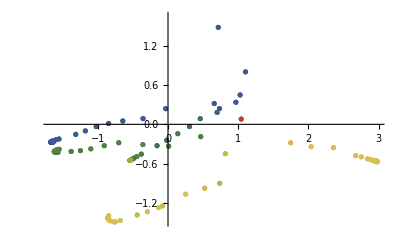

```mathematica
ListPlot[PD,PlotStyle->{RGBColor[0.72987, 0.239399, 0.230961],RGBColor[0.8696881658265921, 0.7043270676283682, 0.32394716443532673],RGBColor[0.8739954580975888, 0.7331538524942828, 0.32549368817882374],RGBColor[0.8658814761867227, 0.7375644740113905, 0.322560781913951],RGBColor[0.8410270503492879, 0.7510749139653102, 0.3135768203955247],RGBColor[0.859131678299899, 0.741233548471106, 0.32012097803881795],RGBColor[0.8525144837120885, 0.7448305420499062, 0.31772910538299143],RGBColor[0.8452698270693142, 0.7487686132489417, 0.31511042825407276],RGBColor[0.8458407381040248, 0.7484582757941988, 0.31531679161164267],RGBColor[0.8456714506618799, 0.7485502975466629, 0.3152556004227683],RGBColor[0.841485047966301, 0.7508259543094258, 0.3137423697022634],RGBColor[0.8510761859640394, 0.7456123760575785, 0.3172092136057672],RGBColor[0.8460707279765938, 0.748333257240816, 0.31539992449824816],RGBColor[0.8360366624012392, 0.7537876033333877, 0.3117729785534105],RGBColor[0.8413946177545323, 0.7508751106228371, 0.3137096825040981],RGBColor[0.8417231760570006, 0.7506965119601322, 0.3138284442556365],RGBColor[0.8194026306021135, 0.7628295779613107, 0.3057603873731892],RGBColor[0.8441518385798461, 0.7493763326328022, 0.3147063165021812],RGBColor[0.8195229115026591, 0.7627641953250328, 0.30580386449830854],RGBColor[0.816427250348703, 0.7644469436778518, 0.30468489675939825],RGBColor[0.7557442170357574, 0.7379805323789776, 0.2915348502529898],RGBColor[0.7069677175380747, 0.713875738827029, 0.28138330788196697],RGBColor[0.7727640614891491, 0.7463915467211358, 0.295077082145318],RGBColor[0.8301732379750539, 0.7569748603697183, 0.3096535661093013],RGBColor[0.7670285889260829, 0.7435571411471535, 0.2938833947478743],RGBColor[0.80392993864197, 0.7617933701888046, 0.30156343778184713],RGBColor[0.829298284336569, 0.7574504701734824, 0.3093373025242976],RGBColor[0.7430565067248007, 0.7317104096591815, 0.2888942378650701],RGBColor[0.8379027202319733, 0.7527732462753097, 0.3124474898799697],RGBColor[0.8263319389900837, 0.7590629246694506, 0.30826507769731937],RGBColor[0.8169855768612, 0.7641434469537226, 0.3048867112746801],RGBColor[0.8239916369857643, 0.7603350727331477, 0.30741914453089575],RGBColor[0.8242960442771878, 0.76016960214617, 0.3075291765795122],RGBColor[0.854219754681691, 0.7439035859741284, 0.31834549816830876],RGBColor[0.81645217530312, 0.7644333948997706, 0.3046939062144062],RGBColor[0.8312668590682717, 0.7563803866848744, 0.31004886994297143],RGBColor[0.8511358711197627, 0.7455799322297542, 0.3172307875960797],RGBColor[0.8222617650135629, 0.7612754014923498, 0.3067938593872473],RGBColor[0.8295902056960082, 0.7572917867251596, 0.30944282136737056],RGBColor[0.30661084498470303, 0.48664539509048754, 0.2678243493300593],RGBColor[0.2938526791309044, 0.47866164791721794, 0.27084637763327923],RGBColor[0.3481925489325801, 0.5126662052255709, 0.25797488603991214],RGBColor[0.2987956807866752, 0.48175485707823357, 0.26967552822766855],RGBColor[0.3121516784981232, 0.4901127127603825, 0.2665118914193479],RGBColor[0.34650542592149397, 0.5116104450383253, 0.2583745150735007],RGBColor[0.30560172538098473, 0.4860139128009484, 0.2680633796137785],RGBColor[0.30824931355618546, 0.4876707085231523, 0.267436245079519],RGBColor[0.32707203527114725, 0.4994495059621528, 0.26297770468914533],RGBColor[0.28001842914215896, 0.45424430078136885, 0.3194628353825441],RGBColor[0.28642615533440047, 0.46707349551606453, 0.2925730839466877],RGBColor[0.30503685826592114, 0.4856604328191986, 0.26819717975627877],RGBColor[0.39382643088575525, 0.5412227689373137, 0.24716558285098753],RGBColor[0.30917640551131165, 0.48825085992272793, 0.26721664469493517],RGBColor[0.3056595267395215, 0.4860500834729805, 0.26804968819892594],RGBColor[0.34785490688986775, 0.5124549171191948, 0.25805486335178646],RGBColor[0.3800947752671187, 0.5326298357535082, 0.2504182017936417],RGBColor[0.37892811746262506, 0.5318997699230795, 0.2506945481702098],RGBColor[0.331867770458447, 0.502450559380341, 0.2618417383098987],RGBColor[0.237736, 0.340215, 0.575113],RGBColor[0.24503571670657479, 0.34236065345607014, 0.56733305687861],RGBColor[0.237736, 0.340215, 0.575113],RGBColor[0.237736, 0.340215, 0.575113],RGBColor[0.24011240084299393, 0.3409135110363509, 0.5725802628904264],RGBColor[0.237736, 0.340215, 0.575113],RGBColor[0.237736, 0.340215, 0.575113],RGBColor[0.24054097551939707, 0.3410394847929462, 0.5721234935746143],RGBColor[0.237736, 0.340215, 0.575113],RGBColor[0.23959381740754793, 0.3407610804167458, 0.5731329623709187],RGBColor[0.237736, 0.340215, 0.575113],RGBColor[0.237736, 0.340215, 0.575113],RGBColor[0.237736, 0.340215, 0.575113],RGBColor[0.237736, 0.340215, 0.575113],RGBColor[0.237736, 0.340215, 0.575113],RGBColor[0.237736, 0.340215, 0.575113],RGBColor[0.23844886195530168, 0.3404245361751116, 0.574353240999948],RGBColor[0.237736, 0.340215, 0.575113],RGBColor[0.24263127220299613, 0.3416538993632181, 0.5698956825568822],RGBColor[0.2382655527614883, 0.3403706549053247, 0.5745486095544854],RGBColor[0.2515639934192704, 0.3442795525111748, 0.560375304468887],RGBColor[0.2583237561534516, 0.37877893939347723, 0.4830108778223839],RGBColor[0.26428140793431626, 0.42198269763468177, 0.3872090281206404],RGBColor[0.2612284646365972, 0.3998433331652103, 0.4363017958274455],RGBColor[0.288514173934268, 0.47125401079148327, 0.2838108023729427],RGBColor[0.28237616264662835, 0.4589648243109133, 0.30956870664091096],RGBColor[0.2674835023382857, 0.4291475641032694, 0.37206512454260815],RGBColor[0.2845991267053834, 0.46341551991531166, 0.3002401321673105],RGBColor[0.35632432011710147, 0.5177548681221085, 0.25604871240676286],RGBColor[0.2755251315618696, 0.44524806905594555, 0.3383187682729989],RGBColor[0.33527622653458955, 0.5045834875672727, 0.2610343769030615],RGBColor[0.38593065850716096, 0.5362817883033605, 0.2490358554181677],RGBColor[0.4624754826129366, 0.5814186858886284, 0.24678818471165606],RGBColor[0.3971973212044433, 0.5433321893948958, 0.24636711964970437],RGBColor[0.5095833683745711, 0.6080731281196481, 0.25186702906667013],RGBColor[0.5127541000212, 0.6098671819630487, 0.25220887528337854],RGBColor[0.5492872590378963, 0.6305382641138049, 0.2561476262046498],RGBColor[0.6422489236833656, 0.6818924439849503, 0.2679137972614112],RGBColor[0.237736, 0.340215, 0.575113],RGBColor[0.237736, 0.340215, 0.575113],RGBColor[0.237736, 0.340215, 0.575113],RGBColor[0.237736, 0.340215, 0.575113],RGBColor[0.237736, 0.340215, 0.575113],RGBColor[0.237736, 0.340215, 0.575113],RGBColor[0.237736, 0.340215, 0.575113],RGBColor[0.237736, 0.340215, 0.575113],RGBColor[0.237736, 0.340215, 0.575113],RGBColor[0.237736, 0.340215, 0.575113],RGBColor[0.237736, 0.340215, 0.575113],RGBColor[0.237736, 0.340215, 0.575113],RGBColor[0.237736, 0.340215, 0.575113],RGBColor[0.237736, 0.340215, 0.575113],RGBColor[0.237736, 0.340215, 0.575113],RGBColor[0.237736, 0.340215, 0.575113],RGBColor[0.237736, 0.340215, 0.575113],RGBColor[0.237736, 0.340215, 0.575113],RGBColor[0.237736, 0.340215, 0.575113],RGBColor[0.789084045455776, 0.43880561979057575, 0.2827219735998753],RGBColor[0.8274152932273967, 0.5663685201194278, 0.3087207964033088],RGBColor[0.8514567052354841, 0.6448282527273054, 0.31738033063263116],RGBColor[0.8684509855256598, 0.7002894996366784, 0.3235015414760695],RGBColor[0.8754026067392908, 0.7323889506070173, 0.3260023206988603],RGBColor[0.861601051295327, 0.7398912396285371, 0.32101356562505595],RGBColor[0.8558804228693497, 0.7430008752062556, 0.31894576868714447],RGBColor[0.8476922851644353, 0.7474518065421971, 0.31598605782801326],RGBColor[0.8389752451988832, 0.7521902400832016, 0.31283516823928054],RGBColor[0.8357770251399115, 0.753928737699231, 0.31167912922533614],RGBColor[0.8263015614440904, 0.7590794373828713, 0.3082540973308441],RGBColor[0.8245745215956776, 0.7600182266481162, 0.3076298358958621],RGBColor[0.8212956675527991, 0.7618005555159694, 0.3064446506601047],RGBColor[0.8176971849735197, 0.7637566289787229, 0.30514393145506546],RGBColor[0.804257921909342, 0.7619554558044168, 0.3016316988516246],RGBColor[0.7945939909678207, 0.7571796505981263, 0.2996204064170752],RGBColor[0.7880564245942926, 0.7539488593484684, 0.2982597843403024],RGBColor[0.7789364664584125, 0.7494418793410522, 0.296361705503326],RGBColor[0.7742856136884456, 0.7471434805831445, 0.29539375311965915]}]
```

```mathematica
ListPlot[PointData,ColorFunction->ColorData[{"DarkRainbow","Reverse"}][#]&/@interpolatedata[[All,2]]]
```

-Graphics-